# research work page

```mathematica
SetDirectory[NotebookDirectory[]];
(*CharAuto[n_]:=If[$CharAuto$n>1,FromCharacterCode[97+n-$CharAuto$n--],Clear[$CharAuto$n];FromCharacterCode[97+n-1],$CharAuto$n=n-1;"a"]*)
CharSeq[i_,{f_,t_,n_}]:=FromCharacterCode[97+Floor[(i-f)/(t-f)*(n-1)]]
```

## 变量定义

symbol | content | range | description
n | 虚拟机数量 | [1,∞) | 是一个整数数
VM_i | 表示第几个虚拟机 | \ | 只表示概念,不参与运算
N | 所有虚拟机内存总和 | \ | 常量
N_i | 当前虚拟机分配的内存 | [0,1] | 以百分表示,乘以Total换算成MB单位
F_i | 当前虚拟机可用内存 | [0,1] | =(Free+Buffer+Cache)/Total
A_i | 当前虚拟机使用的内存 | [0,1] | =1-F_i
A | 使用内存的集合 | \ | ={A_i|i=1...n}
A' | 根据上下文,除去A_i
剩余使用内存的和 | \ | =∑A-A_i

## τ值的推导

### 求解线性方程组

现在先不考虑交换空间.这可以通过假设只研究总内存能够满足分配方案的情况.此时交换空间使用率为0.
即可以满足不用考虑的条件.

原方程组可以重新用矩阵表达:

ΑX=Β

其中Α为(1 | 1 | 1 |   | 1
1 | -1 | 0 | ⋯ | 0
1 | 0 | -1 |   | 0
  | ⋮ |   | ⋱ |  
1 | 0 | 0 |   | -1),Β为(Ν
τ(A_1-A_2)
τ(A_1-A_3)
⋮
τ(A_1-A_n)).n为方程的个数.X=(N_t1
N_t2
N_t3
⋮
N_tn).
现,为了表述方便.左右两边同时除以Ν,使得单位化为1.即Α(X/Ν)=Β/N.
这里需要特别强调.我们约定以下条件.
1.每台虚拟机的初始内存不固定.为物理机内存/虚拟机台数.
2.总内存一直固定为所有物理机内存.
这种设定常常见于实际环境中.为了使利益最大化.希望能够充分使用物理机资源.
解得X为    Α^-1 Β.即

```mathematica
Inverse[({{1, 1, 1, 1}, {1, -1, 0, 0}, {1, 0, -1, 0}, {1, 0, 0, -1}})]//MatrixForm
```

(1/4 | 1/4 | 1/4 | 1/4
1/4 | -3/4 | 1/4 | 1/4
1/4 | 1/4 | -3/4 | 1/4
1/4 | 1/4 | 1/4 | -3/4)

Α^-1 Β=(1/n | 1/n | 1/n |   | 1/n
1/n | 1/n-1 | 1/n | ⋯ | 1/n
1/n | 1/n | 1/n-1 |   | 1/n
  | ⋮ |   | ⋱ |  
1/n | 1/n | 1/n |   | 1/n-1)(1
τ(A_1-A_2)
τ(A_1-A_3)
⋮
τ(A_1-A_n))=(1/n+τ(A_1-1/n∑_(i=1)^n A_i)
1/n+τ(A_2-1/n∑_(i=1)^n A_i)
1/n+τ(A_3-1/n∑_(i=1)^n A_i)
⋮
1/n+τ(A_n-1/n∑_(i=1)^n A_i))

设A=(A_1,A_2,A_3,…,A_n).为整个系统当前使用的内存的向量
其中,当A_i(i=1…n)固定的时候.1/n∑_(i=1)^n A_i为定值.等于Ā.
所以对于N_ti=1/n+τ(A_i-Ā)可以重新表述为.所有内存的平均+当前内存和总的使用内存的平均的差值再乘以一个影响系数.
该方程关于τ是一个线性方程.线性变化的.当前内存A_i 和 Ā的差值要么为正要么为负.乘上τ之后都不改变极性.只会改变幅值.
幅度范围以1/n为中心.上下伸展.

### τ的值域的讨论

当0<τ<1时.和τ=1相比实际上是拉小这种差异性.
τ为0的时候.所有解都取得1/n.τ为1的时候差异性最大.
当τ>1时.实际上是拉大这种差异性.但是会因为幅度范围到达负值.也就是一些情况.会分配负的内存.所以是不可取的.
所以τ的取值范围是(0,1]

```mathematica
X[list_List]:=Table[1/Length[list]+τ(list[[i]]-Mean[list]),{i,1,Length[list]}];
X2=X[{A1,A2}];
X3=X[{A1,A2,A3}];
```

现在以n=2作出图形,任意取A_1和A_2.(这里取A_1=0,A_2=1)

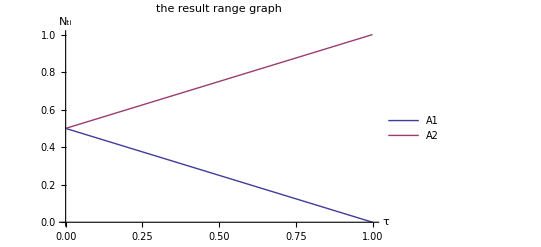

```mathematica
g=Plot[Evaluate[X2/.{A1->0,A2->1}],{τ,0,1},
PlotLabel->"the result range graph",
PlotLegends->{"A1","A2"},AxesLabel->{"τ","N_ti"}]
Export["graph/tau_plot.eps",g];
Export["graph/tau_plot.png",g,ImageResolution->150];
```

可以看出这种变化趋势.

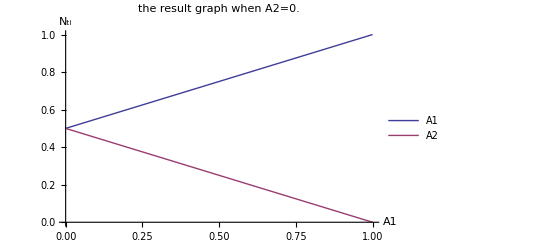
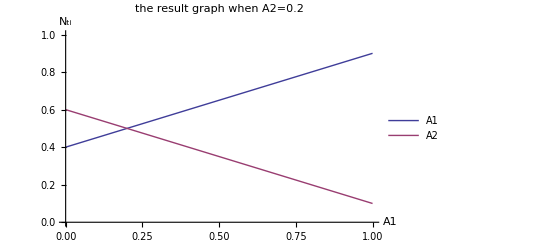
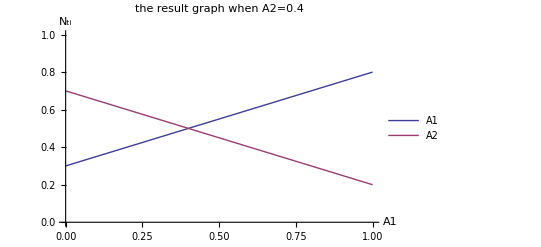
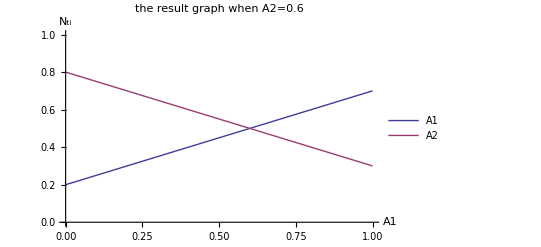
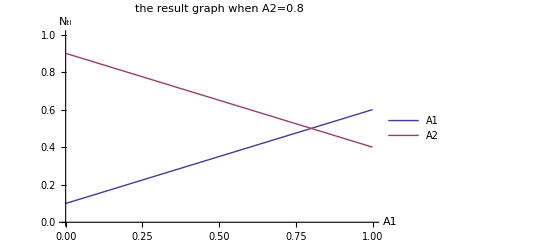
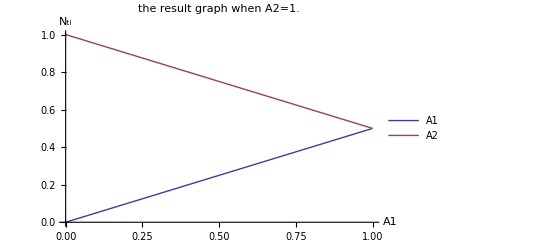

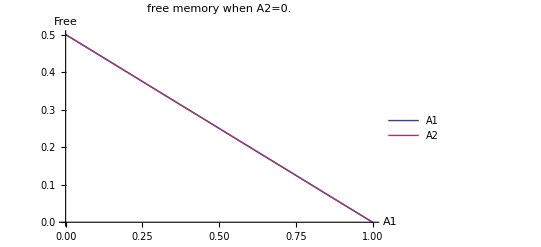
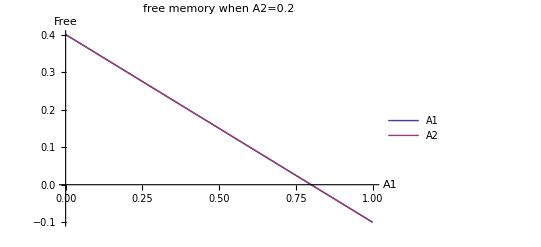

```mathematica
Table[Plot[Evaluate[X2/.{A1->a,A2->b,τ->1}],{a,0,1},PlotLabel->"the result graph when A2="<>ToString[b],PlotRange->{0,1},PlotLegends->{"A1","A2"},AxesLabel->{"A1","N_ti"}],{b,0,1,0.2}]
Table[Plot[Evaluate[(X2/.{A1->a,A2->b,τ->1})-{a,b}],{a,0,1},PlotRange->{{0,1}},PlotLabel->"free memory when A2="<>ToString[b],PlotLegends->{"A1","A2"},AxesLabel->{"A1","Free"}],{b,0,0.8,0.2}]
```

N_ti的求解范围也可以计算出来.可以用一个最大最小值区间来表示.
N_ti的上界即是∀A_i∈[0,1]结果取最大值.由公式可以容易的看出.当A_i=1,A_j=0,j≠i时候N_ti为最大值.N_tj为最小值.
所以可以得到[(1-τ)/n,(1+(n-1)τ)/n]

t

0

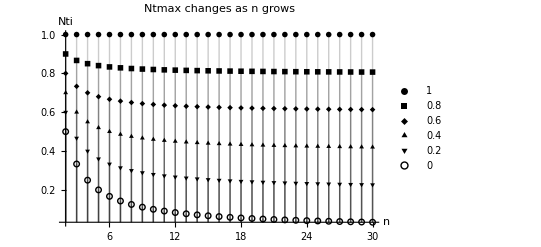
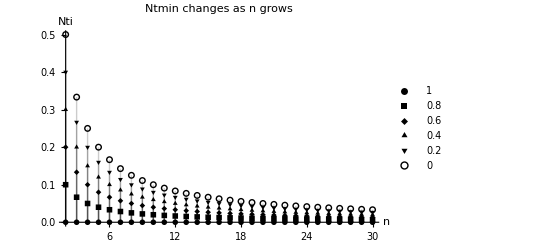

```mathematica
Ntmax[τ_,n_]:=(1+(n-1)τ)/n;
Ntmin[τ_,n_]:=(1-τ)/n;
Limit[Ntmax[t,n],n->Infinity]
Limit[Ntmin[t,n],n->Infinity]

(g=Table[
DiscretePlot[{f[1,n],f[0.8,n],f[0.6,n],f[0.4,n],f[0.2,n],f[0,n]},{n,2,30},
PlotMarkers->{Automatic,Tiny},PlotStyle->Black,PlotLegends->PointLegend[Array[Black,6],{1,0.8,0.6,0.4,0.2,0},LegendMarkers->Automatic],
AxesLabel->{"n","Nti"},PlotLabel->ToString[f]<>" changes as n grows",PlotRange->All
]
,{f,{Ntmax,Ntmin}}])//TableForm
Export["graph/max.eps",g⟦1⟧];
Export["graph/min.eps",g⟦2⟧];
```

根据上图.我们可以得到当n→∞时Ntmax→τ,Ntmin→0所以变化区间并不会因为n的增大而缩小.而最后会稳定到[0,τ]区间.这个是比较好的.

### τ的可行解域的讨论

为了研究不同的τ值的影响.现在我们来从下面一个角度观察.
 >  在总内存能够满足分配的情况下.需要解X的每一个元素N_ti大于等于当前申请的量A_(i.)
 >  也就是分配的结果应该大于申请的容量.
 >  否则.会得出明明还有富余但是分配的反而无法满足提出的需求.这种异常的情况.
所以可以列出条件限制方程组 X≥A 即  Piecewise[{{N_t1≥A_1, □}, {N_t2≥A_2, □}, {⋮, □}, {N_tn≥A_n, □}}]   最后根据τ画出⇔来解区域.称这样的区域为可行解域.
为了方便研究.只画出在n=2时不同τ的可行解域.

```mathematica
Manipulate[RegionPlot[Min[(X2/.{A1->a,A2->b,τ->t})-{a,b}]>0,{a,0,1},{b,0,1}],{{t,0.75},0,2},SaveDefinitions->True]
```

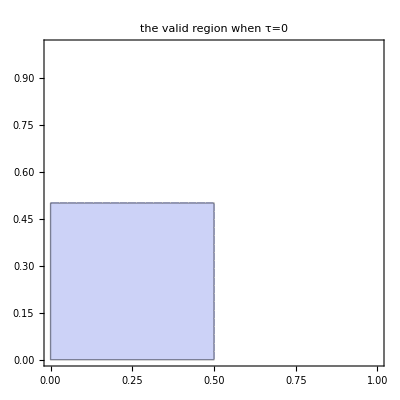

```mathematica
g=RegionPlot[Min[(X2/.{A1->a,A2->b,τ->0})-{a,b}]>0,{a,0,1},{b,0,1},
PlotLabel->"the valid region when τ=0"]
Export["graph/valid_region_0.png",g,ImageResolution->150];
```

这个是τ等于0的时候的结果.可以看到.其中满足解的范围非常小.
特别的.总内存为1,每台虚拟机在初始化的时候各自分配0.5.
要求A_1,A_2≤0.5.也就是每台虚拟机只能提出小于等于各自的初始内存.不能超过它.不然解就会违反判定条件.
这个是非常的不合理的.而且是毫无意义的.
下面再看一下τ从0取到1,间隔0.2的情况

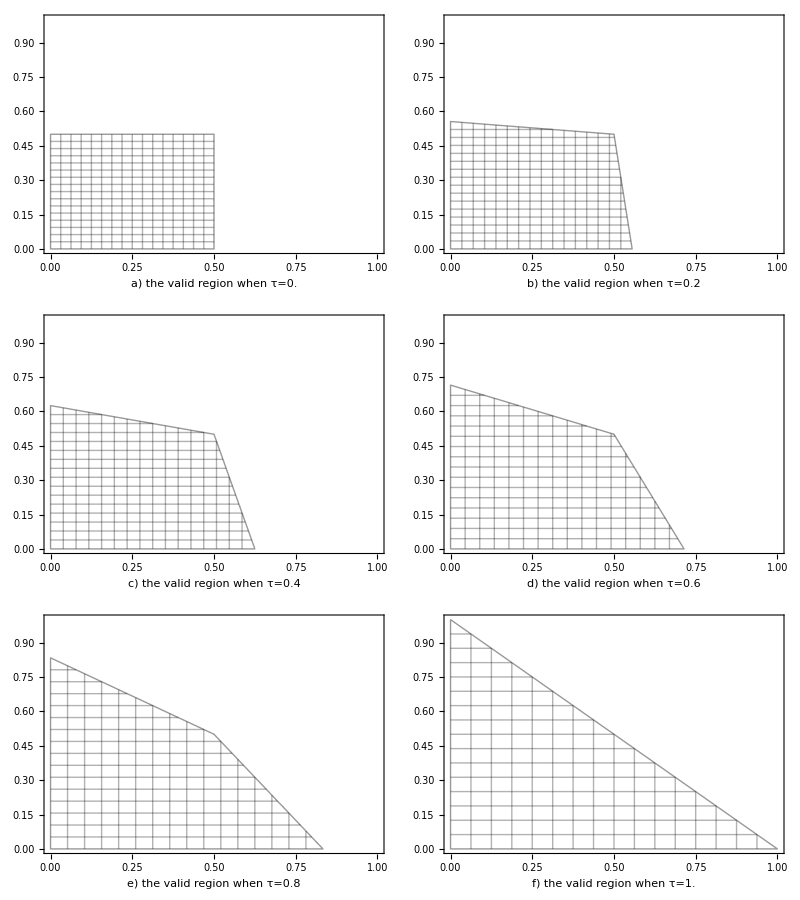

```mathematica
g=Partition[Table[
RegionPlot[Min[(X2/.{A1->a,A2->b,τ->t})-{a,b}]>0,{a,0,1},{b,0,1},
PlotStyle->None,Mesh->True,AxesLabel->{"A1","A2"},
FrameLabel->CharSeq[t,{0,1,6}]<>") the valid region when τ="<>ToString[t]
],{t,0,1,0.2}],2];
g//TableForm
Table[Export["graph/valid_region_table("<>CharSeq[2i-1,{1,6,6}]<>","<>CharSeq[2i,{1,6,6}]<>").eps",GraphicsRow[g⟦i⟧]],{i,3}];
```

由组图可以看出随着τ的增大.可行解域也不断增大.

```mathematica
X2/.{A1->0.7,A2->0.2,τ->0.75}
```

{0.6875,0.3125}

具体来说.不可解的例子,取τ=0.75的图,取A_1=0.7,A_2=0.2.求解得到
X={0.6875,0.3125}对于A_1就出现了异常解.

当τ为1的时候达到最大,满足可分配条件的全域(A_1+A_2≤1)可解

下面观察一下可行解域随着n的增大的变化情况

对于使用的观测条件.N_ti≥A_i,变换一下可以得到N_ti-A_i=F_i≥0,也就是可用内存大于0.
现在重新计算可用内存F_i=(1/n+τ(A_i-Ā))-A_i=1/n-(1-τ)A_i-τ Ā.
特别的.当τ=1时.有F_i=1/n-Ā.即F_i与i无关.即所有的虚拟机的可用内存均相等为总平均与使用平均的差值.
当Ā=1/n,即∑A=1时.即临界条件:所有使用内存等于总可用内存时候.每台虚拟机的剩余内存为0.
这也是为什么τ=1的可行解域非常大的原因.

但是.考虑到在τ=1时候产生的特殊现象,即所有虚拟机的剩余内存均相等.这感觉有些不公平.

下面,研究可行解域和n的关系.因为当n超过2的时候作图就变得困难了.所以需要变换一种方式.
已知可行解域可以表述为F_i≥0,∀i∈[1...n].也就是所有的虚拟机的可用内存都需要大于0.
所以我们只需要研究其中一台的临界条件.只要它不满足.那么可以知道其他的虚拟机无论是否满足.这整个组合都是不满足条件的.于是有F_i≤0,展开1/n-(1-τ)A_i-τ Ā=1/n-(1-τ)A_i-τ((A_i+A')/n)≤0.我们要重新表述成关于A_i的不等式.
因为Ā和A_i是相关的.所以我们必须把Ā展开成两个部分.A_i和A',其中A'定义为∑A_j(j=1...n,j≠i).
所以现在A'和A_i是无关的了.
之后可以得到A_i≤(1-τ A')/(n(1-τ)+τ)即为可行解域.它关于A'是线性的.和n=2的作图是符合的.这个不是重点.我们可以画图如下

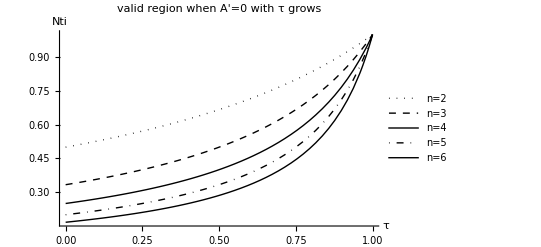

```mathematica
region[n_,τ_,AA_]:=(1-τ AA)/(n(1-τ)+τ);
g=Plot[Evaluate[Table[region[n,τ,0],{n,2,6}]],{τ,0,1},
PlotStyle->{{Black,Dotted},{Black,Dashed},{Black,Thick},{Black,DotDashed},{Black,AbsoluteThickness[1]}},
PlotLegends->{"n=2","n=3","n=4","n=5","n=6"},
AxesLabel->{"τ","Nti"},
PlotLabel->"valid region when A'=0 with τ grows"
]
Export["graph/valid_region_n.eps",g];
```

这个图我们能够非常直观的发现一个事实.就是除了τ=1之外.其他的τ值导致随着n的增加.
可行解域在不断的缩小.缩小的速度在不断的减小.

## ϵ的推导

对于原公式

(1-τ+ϵ(1-SF_i/ST_i))/(Nt_i-τA_i)

已知当解超出可行解域的时候,即F_i<0,就会使用交换空间.从而使得1-SF_i/ST_i>0,在下次计算的时候就需要考虑ϵ的影响了.

### 求解方程组

为了在计算的时候方便.需要重新表达一下公式,令

S_i=1-SF_i/ST_i

其中S_i表示SWAP空间的使用率.

原线性方程组表示为:

((1-τ+ϵ(S1))/(Nt1-τ A1)==(1-τ+ϵ(S2))/(Nt2-τ A2)
(1-τ+ϵ(S1))/(Nt1-τ A1)==(1-τ+ϵ(S3))/(Nt3-τ A3)
⋮
(1-τ+ϵ(S1))/(Nt1-τ A1)==(1-τ+ϵ(Sn))/(Ntn-τ An)
N=∑_(i=1)^n Nt_i

再令

T_i=1-τ+ϵS_i

此时原线性方程组可以化为矩阵形式:

(1 | 1 | 1 |   | 1
T_2 | -T_1 |   | ⋯ |  
T_3 |   | -T_1 |   |  
  | ⋮ |   | ⋱ |  
T_n |   |   |   | -T_1)(Nt_1
Nt_2
Nt_3
⋮
Nt_n)=(N
τ(T_2 A_1-T_1 A_2)
τ(T_3 A_1-T_1 A_3)
□
τ(T_n A_1-T_1 A_n))

```mathematica
LinearSolve[({{1, 1, 1}, {T2, -T1, 0}, {T3, 0, -T1}}),({{1}, {τ(T2 A1-T1 A2)}, {τ(T3 A1-T1 A3)}})];
LinearSolve[({{1, 1, 1, 1}, {T2, -T1, 0, 0}, {T3, 0, -T1, 0}, {T4, 0, 0, -T1}}),({{1}, {τ(T2 A1-T1 A2)}, {τ(T3 A1-T1 A3)}, {τ(T4 A1-T1 A4)}})];
```

该公式比较复杂,利用计算机解得最后得结果为Nt_i=(T_i-T_i τ(∑A_j-A_i)+A_i τ(∑T_j-T_i))/(∑_(j=1)^n T_j),上下上下同除以n可以再得到(T_i/n-T_i τ Ā+A_i τ T̄)/(T̄)= T_i/(T̄)(1/n-τ Ā)+A_i τ,最后化简,得到最终的结果:

Nt_i=(1-τ+ϵS_i)/(1-τ+ϵ S̄)(1/n-τ Ā)+A_i τ

对公式进行简单的讨论:

当∀S_i=0时.就可以退化成只有τ的简单表达式.

而且我们可以看到,和简单表达式相比.

含有ϵ的表达式是将1/n-τ Ā这一部分乘以一个权值.而且这一部分是和i无关的量,只由虚拟机的整体决定.

公式(3)关于A_i依然是线性表达式.但是关于S_i就不是了.所以有必要研究一下关于S_i的变化规律

### ϵ式的系数的讨论

依然先考虑n=2的简单情况.另

k=(1-τ+ϵS_i)/(1-τ+ϵ S̄)

因为ϵ的影响是增加了一个乘积因子k,所以我们需要先研究一下k的变化规律.

下图是研究乘积因子k=的变化规律.只讨论两个虚拟机{VM_1,VM_2}.另VM_2使用的交换空间为定值,τ和ϵ为定值,观察k随VM_1使用的交换空间S_1的变化规律.

```mathematica
KX[S_List]:=Table[(1-τ+ϵ S[[i]])/(1-τ+ϵ Mean[S]),{i,Length[S]}];
EX[A_List,S_List]:=Table[(1-τ+ϵ S[[i]])/(1-τ+ϵ Mean[S])(1/Length[A]-τ Mean[A])+A[[i]]τ,{i,Length[A]}];
KX2=KX[{S1,S2}];
EX2=EX[{A1,A2},{S1,S2}];
```

```mathematica
Manipulate[
Plot[{KX2[[1]]/.{τ->t,ϵ->e,S2->s2},KX2[[2]]/.{τ->t,ϵ->e,S2->s2}},{S1,0,1},
AxesLabel->{"S1","k"},PlotLegends->{"k1","k2"},
PlotLabel->"k change though S1 when τ="<>ToString[t]<>" and ϵ="<>ToString[e]<>" and S2="<>ToString[s2],
PlotRange->{0,2}],
{{t,0.75},0,1},{{e,0.1},0,1},{s2,0,1},
SaveDefinitions->True]
```

该图是两条曲线,我们可以统一的将两条曲线夹角的形状称为开口.

通过分别对τ,ϵ,S_2代入不同的值,绘制图形,我们能够比较容易的发现三个变量之间的控制关系.

ϵ控制开口大小,τ控制开口曲度,S2控制曲线偏移.
当ϵ和τ比较小的时候,曲线接近直线.当ϵ>0,并且τ足够大的时候.开口就会出现比较明显的曲度如下:

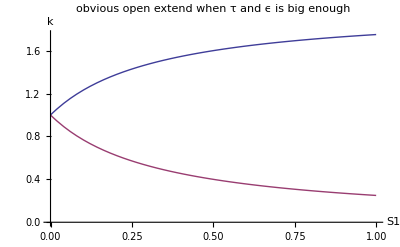

```mathematica
Plot[Evaluate[KX2/.{S2->0,τ->0.9,ϵ->0.6}],{S1,0,1},
AxesLabel->{"S1","k"},PlotLabel->"obvious open extend when τ and ϵ is big enough"]
```

上图中τ取0.9,ϵ取0.6.

继续讨论,我们已经得到了k的变化规律,下一步,讨论对于原来公式中前半部分乘以系数k的之后的变化规律.

因为乘以一个大于1的数之后,必然会导致结果增大.这个比较明显.

所以,我们可以得出,基本上系数k的存在会使得使用内存更多的VM变得更多,是放大效果.

公式的前半部分1/n-τ Ā在总内存能够满足的情况下是大于0的.所以k(1/n-τ Ā)是放大差距.
但是随着使用内存的增加,当τĀ接近1/n时.放大效果会减小.
当总内存不能够满足分配情况时,即τĀ超过1/n时k(1/n-τ Ā)为负,原来的放大效果就会反向成缩小.

考虑实际情况.在Ā,比较小的时候就开始使用Swap分区.说明分配并不是那么合理.
所以可以比较大幅度的调整让使用Swap分区的多分得一些内存.

在Ā比较大的时候.已经没有多少可用内存可供调整了.所以调整幅度要变小一些.

这是和实际情况符合的.

但是当ϵ存在时,τ就绝对不能为1了.因为会出现异常的情况:

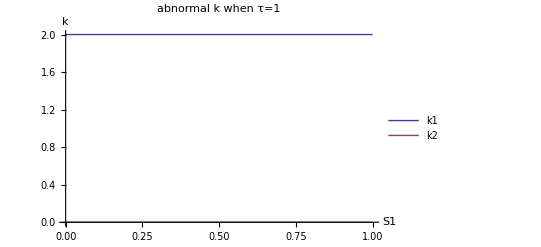

```mathematica
Plot[Evaluate[KX2/.{τ->1,ϵ->0.1,S2->0}],{S1,0,1},
PlotLegends->{"k1","k2"},AxesLabel->{"S1","k"},
PlotLabel->"abnormal k when τ=1"
]
```

当τ为1时.S1和S2均为0时,K是除0式.无意义.不过此时会退化到简单方程所以k应该为1.这个没有问题.
但是当S2为0时,S1无论是多少,ϵ无论是多少.都会得到一个系数为2,另外一个系数为0.
这个情况重新表述即是:不用Swap还好,两个都用Swap也还好,一个使用,一个不使用就会出现异常情况了.
系数为0本身就是一个非常严重的结果了.而且还与S1无关.这个是非常明显的异常情况.

#### ϵ的实际意义

经过上面的讨论,我们可以了解到,其实ϵ可以看作是τ的补充.当τ计算结果不可行的时候.就会使用swap,此时ϵ就有效了.于是会放大结果.
进而达到修正的效果.
另外ϵ补全了总内存不能满足分配的时候.应该如何计算.

虽然这个时候内存不管怎么分配都会使用Swap.
但是至少我们要保证分配方案的连续性和有意义(不能小于0,不能大于总内存)

所以我们可以得到以下定论:
* 当τ比较小时ϵ应该比较大;
* 当τ比较大时ϵ应该比较小;
* 当τ等于1时ϵ必须等于0!!此时公式会完全退化为上面只有τ的讨论的结果.
  因为当τ等于1时,全域可行,也就是理论上完全不会使用swap分区(在总内存可满足的情况下).
  也就是系数虽然是异常的.但是不会启动这个条件.所以k还是1.
  不过实际情况中根本不能保证不使用交换空间.理论并不等于实际.
  
这个是比较好理解的.
τ比较大时,可行解域比较大,当不可行的时候都是已经Ā接近1/n的时候了.所以我们修正需要小一些.
τ比较小的时候,大部分情况都是不可行的.所以我们需要修正程度更大一些.
这也体现了ϵ是作为τ的一个补充的观点.

#### ϵ的震荡现象

为了进一步的简化变量.我们之前只是孤立的考虑了S_i和A_i.但是其实他们之间是如下有联系的.

S_i=max(0,-F_i)=max(0,A_i-N_ti)

其中N_ti是上一次的分配结果.

这个联系是显而易见的.因为上一次的分配方案导致了解在可行域之外.也就是F_i<0,所以内存不够的部分
全部被放到交换空间中去了.从而在下一次的计算中扩大结果.从而下一次的N_ti增大.从而下一次的S_i减小.
从而下下一次的N_ti减小......

所以我们能够非常清楚的看到.这个是一个震荡过程.有震荡必然是不太好的.
我们需要先研究这个现象.然后再想办法解决.

为了研究.我们需要定义N_ti的关于时间的递推表达式.这个表达式中A是固定的,N_ti和S_i都是变化的.
为了结果的准确性和一般性,我们同样需要将A_i和A'区分开来.序列下标使用k是为了和n区分开来.(注意此时的k就不再是系数的含义了.)
有以下定义:

S_i[k] | = | max(0,A_i-N_ti[k])
S'[k] | = | max(0,A'-(1-N_ti[k]))
S̄[k] | = | (S_i[k]+S'[k])/n
N_ti[k+1] | = | (1-τ+ϵS_i[k])/(1-τ+ϵS̄[k])(1/n-τ/n(A_i+A'))+τA_i
N_ti[1] | = | 1/n

我们简单的测试一组解不可行的数据来观察一下震荡现象:
我们可以任意选取一组超出可行域的组合,实际选取的数值为A_i=0.7,A'=0.1,n=2,τ=0.5,ϵ=0.6;

得到结果如下,分别是:

Nti的计算结果序列
Nti’的计算结果序列
Si的使用情况
S’的使用情况
Nti的计算结果序列(图)

Nt[k] 0.5 | 0.682143 | 0.65318 | 0.658197 | 0.65734 | 0.657487 | 0.657462 | 0.657466 | 0.657466 | 0.657466

Nt'[k] 0.5 | 0.317857 | 0.34682 | 0.341803 | 0.34266 | 0.342513 | 0.342538 | 0.342534 | 0.342534 | 0.342534

S_i[k] 0.2 | 0.0178571 | 0.0468198 | 0.0418027 | 0.0426596 | 0.0425129 | 0.042538 | 0.0425337 | 0.0425345 | 0.0425343

S'[k] 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

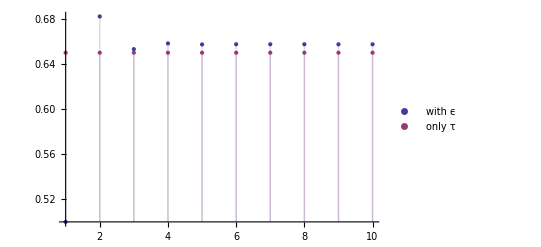

```mathematica
Si[k_]:=Max[0,Ai-Nti[k]]
SS[k_]:=Max[0,AA-(1-Nti[k])]
NtiRc=Nti[k+1]==(1-τ+ϵ Si[k])/(1-τ+ϵ (Si[k]+SS[k])/n)(1/n-τ/n(Ai+AA))+τ Ai;(*Nti result*)
NtiS=1/n-τ/n(Ai+AA)+τ Ai;(*nti static*)
ai=0.7;aa=0.1;nn=2;t=0.5;e=0.6;
nti=RecurrenceTable[{NtiRc/.{τ->t,ϵ->e,Ai->ai,AA->aa,n->nn},Nti[1]==1/nn},Nti,{k,1,10}];
ntt=1-nti;
ntis=NtiS/.{n->nn,τ->t,Ai->ai,AA->aa};

"Nt[k]"Grid[{nti},Frame->All]
"Nt'[k]"Grid[{ntt},Frame->All]
"S_i[k]"Grid[{Max[0,#]&/@(ai-nti)},Frame->All]
"S'[k]"Grid[{Max[0,#]&/@(aa-1+nti)},Frame->All]
ListPlot[{nti,ConstantArray[ntis,10]},
Filling->Bottom,PlotRange->All,
PlotLegends->{"with ϵ","only τ"}
]
```

从数值序列上我们更能够容易的看出震荡的现象.在图上我们只能够观察到前面几组的震荡现象.

我们可以看到震荡现象:第一次结果偏大,第二次结果就减小很多了.第三次结果再中间一点.并且已经收敛了.
震荡现象的存在揭露了一个事实:

我们的初衷是好的.第一次结果的确修正了结果.增大了许多
但是之后由于震荡现象.马上就缩小了影响.立刻回退了.
最后稳定的结果也仅仅只是和没有ϵ的结果相差一点点.

而且.更重要的是.
当仅含有τ的计算结果可行的时候.没有使用Swap所以有ϵ的式子一定是和τ的一样的.
当仅含有τ的计算结果不可行的时候.有ϵ的式子收敛之后.调整幅度会比预想的要小很多.
而且任何时候.调整之后都不能够使得以前使用Swap的结果变成不使用Swap的结果.
只是减少微量的SWAP而已.
SWAP用和不用影响速度很大.用多和用少区别不太大.

所以得出结论:研究ϵ的意义不是很大,甚至没有研究动态τ的意义大.

## 动态τ的研究

### τ的基准曲线的推导

已知.

N_ti=1/n+τ(A_i-Ā)

我们认为一个比较好的结果应该具有下面的一点或几点:
1. 可用内存均分
2. 分配方案方差最小
3. 变化幅度最小
4. τ尽可能的小

其中第1点指向τ=1这个结果.第2,3,4点是等价的.
所以我们从第4点构造:

F_i≥ξ_0⇔min(F)≥ξ_0⇔1/n-τ Ā-(1-τ)max(A)≥ξ_0

其中ξ_0是一个数学概念,表示正要使用交换空间时的最小可用内存.
该值设定的意义是在实际的环境中,操作系统并不会等到可用内存为0的时候才开始使用SWAP分区.
而是当可用内存小于某个额定值之后就开始使用了.所以我们需要在公式中考虑这个因素.才能正确的计算出即将开始使用SWAP分区的临界条件.
ξ_0无法计算出具体的数值,并且也不是一个常数,但是具有一定的范围.

因为F_i∝-A_i.在公式里面,A_i增大,Ā增大.F_i就很快的减小.
于是可以解得

τ≥(ξ_0+max(A)-1/n)/(max(A)-Ā)

记

τ_b=(ξ_0+max(A)-1/n)/(max(A)-Ā)

τ_b为基准曲线.也是一个数学概念,用于简化描述和整理思路不混乱.
要求所有τ≥τ_b时,解可行,不会使用SWAP空间.
τ_b是关于使用内存集合A,n的一个表达式,为了简化分析.只讨论某个A_i变化,(这里不妨设i=1,ξ=0)其他虚拟机A'均为0的情况.

```mathematica
Tb[A_List,ξ0_]:=(ξ0+Max[A]-1/Length[A])/(Max[A]-Mean[A])/;Max[A]≠Mean[A]
Tb[A_List,ξ_]:=0/;Max[A]==Mean[A]
NSeq[n_]:=Module[{a=ConstantArray[0,n]},a[[1]]=x;a]
```

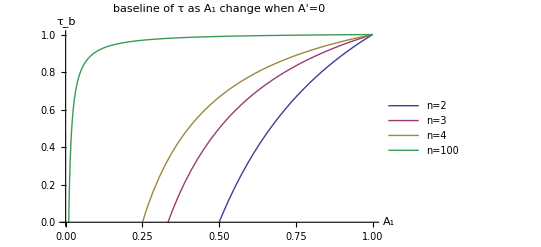

```mathematica
Plot[{Tb[{0,x},0],Tb[{0,0,x},0],Tb[{0,0,0,x},0],Tb[NSeq[100],0]},{x,0,1},PlotLegends->{"n=2","n=3","n=4","n=100"},PlotRange->{0,1},AxesLabel->{"A_1","τ_b"},PlotLabel->"baseline of τ as A_1 change when A'=0"]
```

可以看到随着n的增大,τ_b也在不断的增大,并且变化得越来越剧烈.

### 动态τ曲线的选择

动态τ曲线的选择是多种多样的,只需要保证大于基准曲线.随着不同的动态曲线的选择.分配策略也呈现出不同的具体含义.
我们选择最简单的动态曲线

τ_d=(ξ+max(A)-1/n)/(max(A)-Ā)∈[0,1]

```mathematica
Td[A_List,ξ0_]:=Min[1,Max[0,Tb[A,ξ0]]]
```

作为最后的结果.其中τ_d表示结果dynamic τ的含义.
该曲线所呈现出来的分配策略可以描述为以下几点:

1. 在使用内存比较小时,远没有使用SWAP,不进行分配,每台虚拟机内存均等.
   也就是退化到没有调节的情况,能够最大程度的减少气球驱动的CPU消耗.
2.当可用内存低于预留值的时候,开始分配更多的内存.使得可用内存尽量维持在预留值的水平.
3.当系统总内存再也无法满足分配的时候,采用所有虚拟机可用内存均分的策略.即τ=1的时候.

由此我们可以看到,τ_d动态曲线是尽量保持固定的可用内存的分配策略.

ξ是和ξ_0概念类似的定义,表示最少预留的可用内存.
同ξ_0不同的是,该值是一个计算量.

ξ=f/N

其中f和N都是用内存单位(MB)表示的最小预留可用内存和所有虚拟机总内存.
f是人为设定的数值.需要保证最后ξ>ξ_0,并且严格意义上来说,ξ-ξ_0的这部分内存需要多设置一些.
保证大于当前时刻到下一个时刻使用内存的增长.

这是因为,τ_d是用当前时刻的参数计算出来的数值,最后的结果Nt_i是当前时刻到下一个时刻分配的内存.
τ_d虽然能够保证Nt_i大于当前时刻的可用内存A_i[k],但是随着时间流逝,程序使用更多内存,下一时刻的A_i[k+1]>A_i[k].
Nti并不能保证大于A_i[k+1].所以预留的可用内存应该考虑到这部分增量.即ξ-ξ_0>A_i[k+1]-A_i[k]=ⅆ A_i

不过我们在实际的程序中并不需要考虑得如此复杂.只需要设置一个足够大的f即可.通常100M~150M

(因为对于ξ_0的时候,F=free memory+cached memory.free memory最少60M的时候就不能再少了,cached memory最少30M的时候就不能再少了.所以最小可用内存大约为90M)

最后,τ_d需要强制限定在[0,1]区间之内.以满足意义.

```mathematica
(*
Clear[T];
T[A_List]:= Sqrt[1-(1-Max[A])^2];
Plot[T[{x,0}],{x,0,1},AspectRatio->1,PlotLabel->"1/4 circle curve"]
而且为了保持曲线的连续性需要额外要求从0开始变化.到1为止.曲线光滑连续.(其实是因为作图不好看).
1. 1/4圆曲线 √(1-(x-1)^2),该曲线具有良好的性质
*)
(*T[A_List]:=Max[A](1+0.8(1-(2Max[A]-1)^2))*)
```

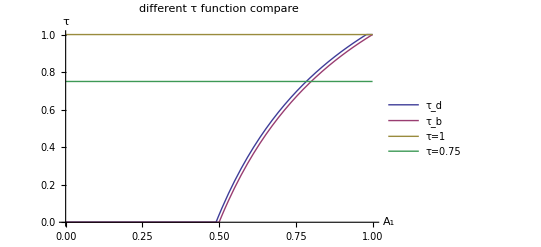

```mathematica
Plot[{Td[NSeq[2],0.01],Max[0,Tb[NSeq[2],0]],1,0.75},{x,0,1},
PlotLegends->{"τ_d","τ_b","τ=1","τ=0.75"},
AxesLabel->{"A_1","τ"},PlotLabel->"different τ function compare"
]
```

该曲线始终高于最低基准.所以能够满足条件.
利用τ_d曲线重新绘制2维和3维的可行解域,可以看到是全域满足的.

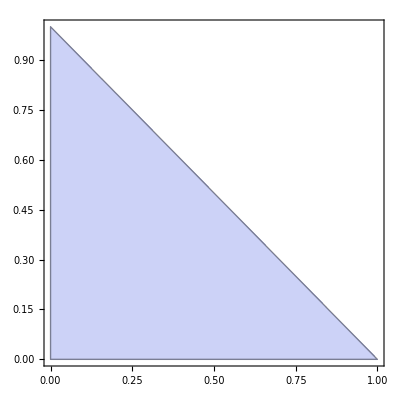

-Graphics3D-

```mathematica
RegionPlot[Min[(X2/.{A1->a,A2->b,τ->Td[{a,b},0.01]})-{a,b}]>=0,{a,0,1},{b,0,1}]
RegionPlot3D[Min[(X3/.{A1->a,A2->b,A3->c,τ->Td[{a,b,c},0.01]})-{a,b,c}]>=0,{a,0,1},{b,0,1},{c,0,1}]
```

```mathematica
Table[Plot[Evaluate[X2/.{A1->a,A2->b,τ->Td[{a,b},0.01]}],{a,0,1},PlotLabel->"the result graph when A2="<>ToString[b],PlotRange->{0,1},PlotLegends->{"A1","A2"},AxesLabel->{"A1","\!\(\*SubscriptBox[\(N\), \(ti\)]\)"}],{b,0,1,0.2}];
Table[Plot[Evaluate[(X2/.{A1->a,A2->b,τ->Td[{a,b},0.01]})-{a,b}],{a,0,1},PlotRange->{{0,1}},PlotLabel->"free memory when A2="<>ToString[b],PlotLegends->{"A1","A2"},AxesLabel->{"A1","Free"}],{b,0,0.8,0.2}];
```

由上,我们先通过分析τ需要满足的条件,得道τ基准曲线,后再根据基准曲线,结合实际环境可能出现的问题.得到一个比较好的动态τ曲线.
再验证动态τ是满足条件的.

最后,在实验环境中通过和τ=1.0的静态曲线的比较而证明,动态τ曲线能够保证运行时间最短,尽量不使用SWAP分区的同时,分配得尽可能的集中,不出现大幅调整的情况.能够满足实际环境的需求.

### 动态τ的下降滞带

另外,
在实验中观测到的内存分配曲线都呈现锯齿波的特征.这是非常好理解的:

1.测试是顺序程序.执行完一个测试程序之后再执行下一个测试程序
2.程序在运行时候,随着程序的运行不断的申请内存.所以在开始是缓慢上升的.
3.程序在退出的时候.所有内存都被释放.导致分配曲线迅速地垂直下降

在实际环境中也会不同程度的体现该现象.
该现象并不影响测试程序的执行和内存调节服务的运行.但是会对气球驱动造成压力,因为这需要指定气球驱动迅速的膨胀和收缩.
所以我们可以设法减缓下降趋势,在上一个程序的内存释放和下一个程序的内存申请之间提供一定的缓冲.
但是上升趋势我们可以不用管.因为我们没有必要剥夺程序申请的内存量.

在静态τ时候.我们能够观测的只有内存分配的最后结果.并且在同一时刻,对于所有虚拟机而言.有总内存上升的就必然有总内存下降的.
所以我们无法实现下降滞带,因为对某一个虚拟机内存的下降滞带就必然导致对另外一些虚拟机的上升滞带.

但是在动态τ的时候.我们还可以全局统一地观测τ的变化.并且对于τ设计下降滞带非常容易:

τ=τ_-1-(τ_-1-τ_d)/γ;(τ_-1>τ_d)

```mathematica
τLocal=0;
γ=10;
BeginTdown[]:=τLocal=0;
Tdown[A_List,ξ0_]:=Module[
{τ},
τ=N[Td[A,ξ0]];
τ=If[τLocal>τ,N[τLocal-(τLocal-τ)/γ],τ];
τLocal = N[τ];
N[τ]
]
EndTdown[]:=τLocal=0;
```

其中τ_-1是上一次运算得出的τ的结果,γ是下降滞带,γ越大,下降速度越慢,实验取γ=10.τ_d是这一时刻计算出来的τ值.

下面证明下降滞带并不会导致结果变差:

∵τ_-1≥τ_d≥τ_b and τ=τ_-1-(τ_-1-τ_d)/γ≥τ_d

∴τ≥τ_b

因为下降滞带之后的τ依然大于τ_b,所以是可行的.不会造成内存分配不足的错误情况.

## 数据模拟

### mono test simulate

mono测试是指定一个范围。并且从低到高的提出内存申请。再由高到低的释放内存。
mono测试简单直观,能够看清楚一个内存申请释放周期的分配结果.
首先看静态τ的简单的内存分配

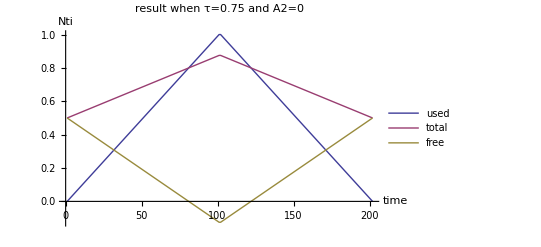

```mathematica
tau=0.75;
a2=0;
used=Range[0,1,0.01]~Join~Range[1,0,-0.01];
total=(X2/.{A1->#,A2->a2,τ->tau})[[1]]&/@used;
ListLinePlot[{used,total,total-used},
PlotLegends->{"used","total","free"},
PlotLabel->"result when τ="<>ToString[tau]<>" and A2="<>ToString[a2],
AxesLabel->{"time","Nti"}
]
Clear[tau,a2,used,total]
```

可以看到当使用内存在1.0附近的时候,分配的结果是不可行的,可用内存也为负值了.

下面使用动态的τ来模拟结果.

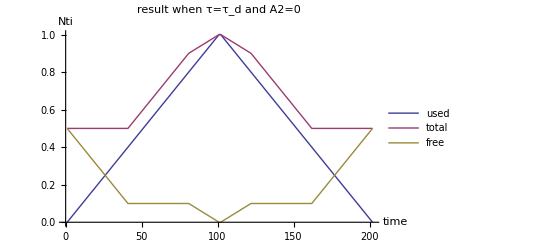

```mathematica
a2=0;
used=Range[0,1,0.01]~Join~Range[1,0,-0.01];
total=(X2/.{A1->#,A2->a2,τ->Td[{#,a2},0.1]})[[1]]&/@used;
ListLinePlot[{used,total,total-used},
PlotLegends->{"used","total","free"},
PlotLabel->"result when τ=τ_d and A2="<>ToString[a2],
AxesLabel->{"time","Nti"}
]
Clear[a2,used,total]
```

虽然图比较丑陋,但是动态τ的分配是可行的.并且体现出来分配策略的三个阶段.

最后再看一下有下降滞带的动态τ分配.

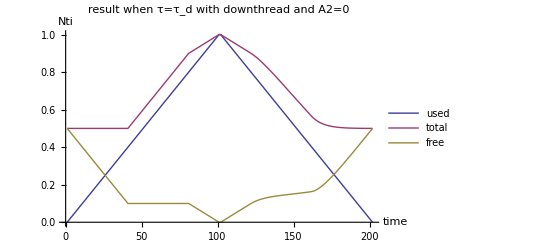

```mathematica
a2=0;
used=Range[0,1,0.01]~Join~Range[1,0,-0.01];
BeginTdown[];
total=(X2/.{A1->#,A2->a2,τ->Tdown[{#,a2},0.1]})[[1]]&/@used;
EndTdown[];
ListLinePlot[{used,total,total-used},
PlotLegends->{"used","total","free"},
PlotLabel->"result when τ=τ_d with downthread and A2="<>ToString[a2],
AxesLabel->{"time","Nti"}
]
Clear[a2,used,total]
```

虽然图比较丑陋,但是有下降滞带的动态τ的分配也是是可行的.
在上升阶段和动态τ是一样的.
但是在下降阶段进行了一些优化,是缓慢的下降.进行一定的时间缓冲.
虽然在mono测试中体现不出来这种处理的好处,但是在接下来的random模拟中就能够体会到加入这种处理带来的好处.

### random test simulate

random测试和mono类似,但是是用一种随机数来表示使用量.更加接近实际环境中的情况.

在静态的τ时候,

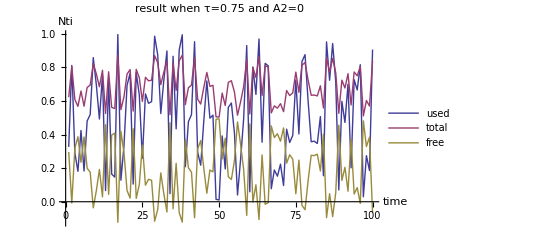

```mathematica
tau=0.75;
a2=0;
used=RandomReal[1,100];
total=(X2/.{A1->#,A2->a2,τ->tau})[[1]]&/@used;
ListLinePlot[{used,total,total-used},
PlotLegends->{"used","total","free"},
PlotLabel->"result when τ="<>ToString[tau]<>" and A2="<>ToString[a2],
AxesLabel->{"time","Nti"}
]
Clear[tau,a2,used,total]
```

同样可以看出,在一些数值的时候分配结果不可行.所以排除.

而对比动态τ和带下降滞带的动态τ,不容易看出什么差别.

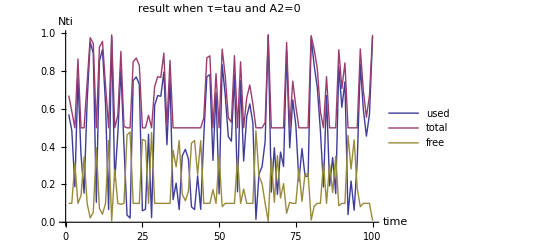

| used | result
mean | 0.462602 | 0.648225
σ | 0.286042 | 0.176244

```mathematica
a2=0;
used=RandomReal[1,100];
total=(X2/.{A1->#,A2->a2,τ->Td[{#,a2},0.1]})[[1]]&/@used;
ListLinePlot[{used,total,total-used},
PlotLegends->{"used","total","free"},
PlotLabel->"result when τ="<>ToString[tau]<>" and A2="<>ToString[a2],
AxesLabel->{"time","Nti"}
]
TableForm[{Mean[{used,total}ᵀ],StandardDeviation[{used,total}ᵀ]},TableHeadings->{{"mean","σ"},{"used","result"}}]
Clear[a2,used,total]
```

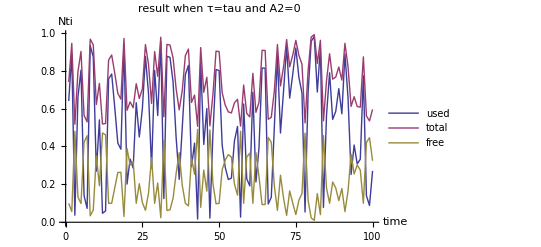

| used | result
mean | 0.523879 | 0.739993
σ | 0.286033 | 0.14945

```mathematica
a2=0;
used=RandomReal[1,100];
BeginTdown[];
total=(X2/.{A1->#,A2->a2,τ->Tdown[{#,a2},0.1]})[[1]]&/@used;
EndTdown[];
ListLinePlot[{used,total,total-used},
PlotLegends->{"used","total","free"},
PlotLabel->"result when τ="<>ToString[tau]<>" and A2="<>ToString[a2],
AxesLabel->{"time","Nti"}
]
TableForm[{Mean[{used,total}ᵀ],StandardDeviation[{used,total}ᵀ]},TableHeadings->{{"mean","σ"},{"used","result"}}]
Clear[a2,used,total]
```

需要从数值上看,带下降滞带的动态τ的整体分配的平均结果高于没有下降滞带的.
并且标准差要更小一些,分配结果的碎片化程度要更小一些.

## not used

#### the research about τ value.

既然τ是线性变化的.所以在τ表达了一种变化范围的思想.当τ为0时.没有变化.当τ为1.时变化程度最剧烈.
所以可以求得基于τ的最大值和最小值.它们之间就是整个可变范围.

```mathematica
manu[A1,A2,τ]
```

{1+(A1 τ)/2-(A2 τ)/2,1-(A1 τ)/2+(A2 τ)/2}

```mathematica
manu3[A1,A2,A3,tau]//Expand
```

{1+(2 A1 tau)/3-(A2 tau)/3-(A3 tau)/3,1-(A1 tau)/3+(2 A2 tau)/3-(A3 tau)/3,1-(A1 tau)/3-(A2 tau)/3+(2 A3 tau)/3}

当A1取最大,A2取最小时.就可以得到最大值,最小值集合了.再考虑一般解的情况.可以得出
一台虚拟机占用全部内存,其他虚拟机都为0时候就是范围集合.

```mathematica
range[τ_,n_]:={1+(n-1) τ,1-τ }
```

画出图像来

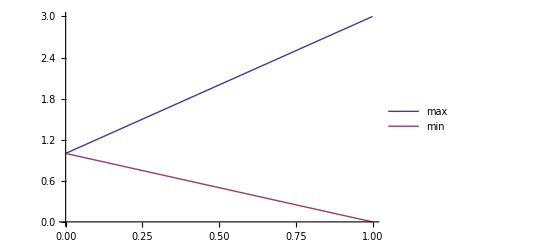

```mathematica
Plot[Evaluate[range[τ,3]],{τ,0,1},PlotLegends->{"max","min"}]
```

其中.非常明显的是,增加虚拟机的台数.只能增加最大值范围.也就是增加上界范围.但是下界范围却和虚拟机台数无关.

现在考虑τ=1的情况,会发现一个比较重要的事实.就是最小值为0.也就是说.可能会有虚拟机完全得不到内存.
在数学意义上.申请内存为0是完全可能的.这个时候理应该给它分配0.但是.事实上.一个运行操作系统的虚拟机不能够分配
0内存.这个和SWAP分区无关.
操作系统运行需要一个最小内存.来存放核心相关的内容.
也就是说要保证一台虚拟机的运行.不能够只是给他分配0内存.然后希望它把所有的运行需要的内存丢到
SWAP分区中.首先不考虑这样带来的巨大的性能损失.重要的是这个是完全不被允许的.
另外一方面.当不断的给一个运行的虚拟机减少分配的总内存的时候.当小于运行最小内存时.系统就会崩溃.造成KernelPanic.
所以虽然在数学意义上τ=1是具有全域可解的很好的性能.但是在这种情况下.会导致过度分配.导致分配0内存.所以需要一个
约束条件来限定它.也就是受保护的最小运行需要内存.作为τ的上界.
其计算公式为τ_up=1-系统最小内存/初始分配内存.因为在上面的计算中.为了简化表达.用1代表每台虚拟机初始分配内存.所以可用的总内存N=n*1.
为了换算成实际内存的MB单位.需要乘以初始内存(一般512~1024M).

```mathematica
tauUp[min_,cur_]:=1-min/cur
```

一般一个系统的最小运行内存和系统有关.运行X的Linux系统典型内存是512MB.现在很多系统要求最小1024MB.
不运行X的Linux服务器系统典型内存是192MB.一般可以分配256MB.
所以可以画出图像来:

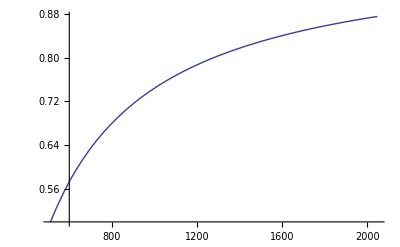

```mathematica
Plot[tauUp[256,m],{m,512,2048}]
```

在典型的初始内存1024MB,最小内存256MB的情况下.τ的上界即为0.75.

总结:通过设置τ为0.75.可以保证在具有尽可能大的可行解域范围的情况下.保护分配的最小内存.从而使得虚拟机能够正常运行.

bug:虽然tau为0.75的时候具有保护策略.但是这个是建立在某一台虚拟机提出申请0内存的情况下.
一般虚拟机正常运行之后,就不可能提出0内存.至少都是最小运行内存.所以提出0这一个条件是永远不可能满足的.
如果真要利用它.可能需要提出保护的最小可用内存.也就是让free memory不能低于某一个值.不过就算低于某一个值.也只是会加剧利用SWAP分区